```mathematica
pn[s_]:=FindInstance[Table[Total[Table[Subscript[a, i]*j^(i-1),{i,1,Length[s]}]]==s[[j]],{j,1,Length[s]}],Table[Subscript[a, i],{i,1,Length[s]}],Reals]
i[in_]:=Table[Last[Flatten[in][[i]]],{i,1,Length[Flatten[in]]}]
po[s_]:=Total[Table[(s[[i]])*j^(i-1),{i,1,Length[s]}]]
```

{{a_1→302867074940665856,a_2→-265105092950347706134396788345570497837/193690281515374794150,a_3→65896526873911761231209169453105633401208045568/23148707568414059974597880625,a_4→-23602484031507742952630776335336581517307518386176/6434290399682973733737911454375,a_5→605453148171815834196134021900944378322493646808547328/182511735646399397784868052600844975,a_6→-14679047676770615726554633348608194059419307680817217536/6503529041698621074913284679781240625,a_7→144378284637661269178129449073598783435206061760391501840384/119502346141212162251531605990980296484375,a_8→-65391378122125365364358327015999276870313340058273098760192/124587552359987147879256355182085841015625,a_9→19302243864381680114698533137841088288555291684834675523584/101935270112716757355755199694433869921875,a_10→-33850302576747201113319659653890635481050321286802178048/586239188593954206094750400819150390625,a_11→4138215078560991389777839867026954956391463172040216571543552/274228036444536928755971868743178073974609375,a_12→-190666762570104071625936104609263103706097787578629226496/55778975478582330074440003134418212890625,a_13→793412628924757048675297354272457760215807943343365095424/1171358485050228931563240065822782470703125,a_14→-7822353034458924586175403905753212507689777594744832/66111746787757327320642454833779296875,a_15→13724618517432055789916969225144025120507387493277696/748395969354134401789809078107958984375,a_16→-14489949006733751112581885900228691294232423038107648/5713943829513311861284097882062353515625,a_17→13238860636532229522705586680492886191677585503142592512/42117479967342621729525085488681607763671875,a_18→-1978849238594166030879198433679030569204417512448/56431146131751058008211167865927734375,a_19→634379231768493617928389582845616309363166296576/179553646782844275480671897755224609375,a_20→-6889816925860341129753515761059282209393017750016/21366883967158468782199955832871728515625,a_21→119351486651851563109736771523789708978121071247616/4465678749136119975479790769070191259765625,a_22→-796418668115988349063723062928252274520715456/395018022922257406057478175061494140625,a_23→36430031975113447550570906410270647743433260512/262686985243301175028222986415893603515625,a_24→-136957849244165986162473870545025656774272/15721287045502494166510442660595703125,a_25→13931921789645482879800109165088594952164768/27842399357584917168889993951914990234375,a_26→-35359468159492412083271446271386504636996/1344115831055823587463654880437275390625,a_27→50377299962198577052127756386125391762/39766740563781762942711682853173828125,a_28→-53674380900255636666878135517342327626/960082736468445419616896343169482421875,a_29→17962612550218715017328391921823260134/7942502638057139380467051566220263671875,a_30→-6065003257550827662270373922684044/72317920409311473165948036238740234375,a_31→396787187113694272487837206328914564/139211996787924585844449969759574951171875,a_32→-4018881466601727448329593770054676/45290859524707099142797066623429931640625,a_33→3321354802912363607216861138648231/1313434926216505875141114932079468017578125,a_34→-89925651030688940246506661917/1364607715549616493653106422939707031250,a_35→411970732375299489470415288334/262686985243301175028222986415893603515625,a_36→-163222604595923327692848062/4796647421198839930697949268603857421875,a_37→22556475877209895224232726/33576531948391879514885644880227001953125,a_38→-1231548836055219534979976/102309667936864668168886847340926982421875,a_39→13266521728682747460088/67967961216798206126183569911804638671875,a_40→-208353059827079672/73005328911705914206427035351025390625,a_41→4734196746054227940032/126352439902027865188575256466044823291015625,a_42→-102103687331515888/232359274993637249281524355914233583984375,a_43→260458581118700098/56928022373441126073973467198987228076171875,a_44→-65384387442681322/1557757703127798086206001238808650513720703125,a_45→5759724985069138/17135334734405778948266013626895155650927734375,a_46→-1136950437316/489580992411593684236171817911290161455078125,a_47→5373540989708/394112698891332915810118313418588579971337890625,a_48→-25206710156/378026466283523409042358382258646188952099609375,a_49→63566858/240562296725878533026955334164593029333154296875,a_50→-384301/471502101582721924732832454962602337492982421875,a_51→2474/1347849042985951448040841217408686515702392578125,a_52→-4226/1574480232070874998661422662107261376985494873046875,a_53→274/143277701118449624878189462251760785305680033447265625}}

{302867074940665856,-265105092950347706134396788345570497837/193690281515374794150,65896526873911761231209169453105633401208045568/23148707568414059974597880625,-23602484031507742952630776335336581517307518386176/6434290399682973733737911454375,605453148171815834196134021900944378322493646808547328/182511735646399397784868052600844975,-14679047676770615726554633348608194059419307680817217536/6503529041698621074913284679781240625,144378284637661269178129449073598783435206061760391501840384/119502346141212162251531605990980296484375,-65391378122125365364358327015999276870313340058273098760192/124587552359987147879256355182085841015625,19302243864381680114698533137841088288555291684834675523584/101935270112716757355755199694433869921875,-33850302576747201113319659653890635481050321286802178048/586239188593954206094750400819150390625,4138215078560991389777839867026954956391463172040216571543552/274228036444536928755971868743178073974609375,-190666762570104071625936104609263103706097787578629226496/55778975478582330074440003134418212890625,793412628924757048675297354272457760215807943343365095424/1171358485050228931563240065822782470703125,-7822353034458924586175403905753212507689777594744832/66111746787757327320642454833779296875,13724618517432055789916969225144025120507387493277696/748395969354134401789809078107958984375,-14489949006733751112581885900228691294232423038107648/5713943829513311861284097882062353515625,13238860636532229522705586680492886191677585503142592512/42117479967342621729525085488681607763671875,-1978849238594166030879198433679030569204417512448/56431146131751058008211167865927734375,634379231768493617928389582845616309363166296576/179553646782844275480671897755224609375,-6889816925860341129753515761059282209393017750016/21366883967158468782199955832871728515625,119351486651851563109736771523789708978121071247616/4465678749136119975479790769070191259765625,-796418668115988349063723062928252274520715456/395018022922257406057478175061494140625,36430031975113447550570906410270647743433260512/262686985243301175028222986415893603515625,-136957849244165986162473870545025656774272/15721287045502494166510442660595703125,13931921789645482879800109165088594952164768/27842399357584917168889993951914990234375,-35359468159492412083271446271386504636996/1344115831055823587463654880437275390625,50377299962198577052127756386125391762/39766740563781762942711682853173828125,-53674380900255636666878135517342327626/960082736468445419616896343169482421875,17962612550218715017328391921823260134/7942502638057139380467051566220263671875,-6065003257550827662270373922684044/72317920409311473165948036238740234375,396787187113694272487837206328914564/139211996787924585844449969759574951171875,-4018881466601727448329593770054676/45290859524707099142797066623429931640625,3321354802912363607216861138648231/1313434926216505875141114932079468017578125,-89925651030688940246506661917/1364607715549616493653106422939707031250,411970732375299489470415288334/262686985243301175028222986415893603515625,-163222604595923327692848062/4796647421198839930697949268603857421875,22556475877209895224232726/33576531948391879514885644880227001953125,-1231548836055219534979976/102309667936864668168886847340926982421875,13266521728682747460088/67967961216798206126183569911804638671875,-208353059827079672/73005328911705914206427035351025390625,4734196746054227940032/126352439902027865188575256466044823291015625,-102103687331515888/232359274993637249281524355914233583984375,260458581118700098/56928022373441126073973467198987228076171875,-65384387442681322/1557757703127798086206001238808650513720703125,5759724985069138/17135334734405778948266013626895155650927734375,-1136950437316/489580992411593684236171817911290161455078125,5373540989708/394112698891332915810118313418588579971337890625,-25206710156/378026466283523409042358382258646188952099609375,63566858/240562296725878533026955334164593029333154296875,-384301/471502101582721924732832454962602337492982421875,2474/1347849042985951448040841217408686515702392578125,-4226/1574480232070874998661422662107261376985494873046875,274/143277701118449624878189462251760785305680033447265625}

302867074940665856-(265105092950347706134396788345570497837 j)/193690281515374794150+(65896526873911761231209169453105633401208045568 j^2)/23148707568414059974597880625-(23602484031507742952630776335336581517307518386176 j^3)/6434290399682973733737911454375+(605453148171815834196134021900944378322493646808547328 j^4)/182511735646399397784868052600844975-(14679047676770615726554633348608194059419307680817217536 j^5)/6503529041698621074913284679781240625+(144378284637661269178129449073598783435206061760391501840384 j^6)/119502346141212162251531605990980296484375-(65391378122125365364358327015999276870313340058273098760192 j^7)/124587552359987147879256355182085841015625+(19302243864381680114698533137841088288555291684834675523584 j^8)/101935270112716757355755199694433869921875-(33850302576747201113319659653890635481050321286802178048 j^9)/586239188593954206094750400819150390625+(4138215078560991389777839867026954956391463172040216571543552 j^10)/274228036444536928755971868743178073974609375-(190666762570104071625936104609263103706097787578629226496 j^11)/55778975478582330074440003134418212890625+(793412628924757048675297354272457760215807943343365095424 j^12)/1171358485050228931563240065822782470703125-(7822353034458924586175403905753212507689777594744832 j^13)/66111746787757327320642454833779296875+(13724618517432055789916969225144025120507387493277696 j^14)/748395969354134401789809078107958984375-(14489949006733751112581885900228691294232423038107648 j^15)/5713943829513311861284097882062353515625+(13238860636532229522705586680492886191677585503142592512 j^16)/42117479967342621729525085488681607763671875-(1978849238594166030879198433679030569204417512448 j^17)/56431146131751058008211167865927734375+(634379231768493617928389582845616309363166296576 j^18)/179553646782844275480671897755224609375-(6889816925860341129753515761059282209393017750016 j^19)/21366883967158468782199955832871728515625+(119351486651851563109736771523789708978121071247616 j^20)/4465678749136119975479790769070191259765625-(796418668115988349063723062928252274520715456 j^21)/395018022922257406057478175061494140625+(36430031975113447550570906410270647743433260512 j^22)/262686985243301175028222986415893603515625-(136957849244165986162473870545025656774272 j^23)/15721287045502494166510442660595703125+(13931921789645482879800109165088594952164768 j^24)/27842399357584917168889993951914990234375-(35359468159492412083271446271386504636996 j^25)/1344115831055823587463654880437275390625+(50377299962198577052127756386125391762 j^26)/39766740563781762942711682853173828125-(53674380900255636666878135517342327626 j^27)/960082736468445419616896343169482421875+(17962612550218715017328391921823260134 j^28)/7942502638057139380467051566220263671875-(6065003257550827662270373922684044 j^29)/72317920409311473165948036238740234375+(396787187113694272487837206328914564 j^30)/139211996787924585844449969759574951171875-(4018881466601727448329593770054676 j^31)/45290859524707099142797066623429931640625+(3321354802912363607216861138648231 j^32)/1313434926216505875141114932079468017578125-(89925651030688940246506661917 j^33)/1364607715549616493653106422939707031250+(411970732375299489470415288334 j^34)/262686985243301175028222986415893603515625-(163222604595923327692848062 j^35)/4796647421198839930697949268603857421875+(22556475877209895224232726 j^36)/33576531948391879514885644880227001953125-(1231548836055219534979976 j^37)/102309667936864668168886847340926982421875+(13266521728682747460088 j^38)/67967961216798206126183569911804638671875-(208353059827079672 j^39)/73005328911705914206427035351025390625+(4734196746054227940032 j^40)/126352439902027865188575256466044823291015625-(102103687331515888 j^41)/232359274993637249281524355914233583984375+(260458581118700098 j^42)/56928022373441126073973467198987228076171875-(65384387442681322 j^43)/1557757703127798086206001238808650513720703125+(5759724985069138 j^44)/17135334734405778948266013626895155650927734375-(1136950437316 j^45)/489580992411593684236171817911290161455078125+(5373540989708 j^46)/394112698891332915810118313418588579971337890625-(25206710156 j^47)/378026466283523409042358382258646188952099609375+(63566858 j^48)/240562296725878533026955334164593029333154296875-(384301 j^49)/471502101582721924732832454962602337492982421875+(2474 j^50)/1347849042985951448040841217408686515702392578125-(4226 j^51)/1574480232070874998661422662107261376985494873046875+(274 j^52)/143277701118449624878189462251760785305680033447265625

-Graphics-

{{a_1→13631488,a_2→-1387334631423457/29099070,a_3→3501096682348544/48243195,a_4→-78237724981374976/1206079875,a_5→24629939165842432/638512875,a_6→-37934652800768/2321865,a_7→2686234951158944/522419625,a_8→-7104655960638128/5746615875,a_9→34089095149744/147349125,a_10→-1004893123816/29469825,a_11→53392622902/13395375,a_12→-54573662557/147349125,a_13→12067875508/442047375,a_14→-1821841942/1149323175,a_15→137074244/1915538625,a_16→-428006/174139875,a_17→10799/174139875,a_18→-14107/13025662650,a_19→1142/97692469875,a_20→-109/1856156927625}}

{13631488,-1387334631423457/29099070,3501096682348544/48243195,-78237724981374976/1206079875,24629939165842432/638512875,-37934652800768/2321865,2686234951158944/522419625,-7104655960638128/5746615875,34089095149744/147349125,-1004893123816/29469825,53392622902/13395375,-54573662557/147349125,12067875508/442047375,-1821841942/1149323175,137074244/1915538625,-428006/174139875,10799/174139875,-14107/13025662650,1142/97692469875,-109/1856156927625}

13631488-(1387334631423457 j)/29099070+(3501096682348544 j^2)/48243195-(78237724981374976 j^3)/1206079875+(24629939165842432 j^4)/638512875-(37934652800768 j^5)/2321865+(2686234951158944 j^6)/522419625-(7104655960638128 j^7)/5746615875+(34089095149744 j^8)/147349125-(1004893123816 j^9)/29469825+(53392622902 j^10)/13395375-(54573662557 j^11)/147349125+(12067875508 j^12)/442047375-(1821841942 j^13)/1149323175+(137074244 j^14)/1915538625-(428006 j^15)/174139875+(10799 j^16)/174139875-(14107 j^17)/13025662650+(1142 j^18)/97692469875-(109 j^19)/1856156927625

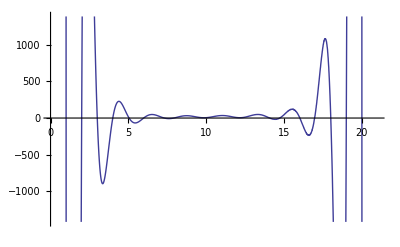

{{a_1→6488064,a_2→-34204034199739/1531530,a_3→1147799763226112/34459425,a_4→-58867437101056/2027025,a_5→1529229511743776/91216125,a_6→-97313523169904/14189175,a_7→916350158360048/442047375,a_8→-95353384904/200475,a_9→1774795895342/21049875,a_10→-1488960943/127575,a_11→2426742476/1913625,a_12→-42497888/392931,a_13→3183492608/442047375,a_14→-6749668/18243225,a_15→3931192/273648375,a_16→-7432/18243225,a_17→311/39092625,a_18→-83/868377510,a_19→4/7514805375}}

{6488064,-34204034199739/1531530,1147799763226112/34459425,-58867437101056/2027025,1529229511743776/91216125,-97313523169904/14189175,916350158360048/442047375,-95353384904/200475,1774795895342/21049875,-1488960943/127575,2426742476/1913625,-42497888/392931,3183492608/442047375,-6749668/18243225,3931192/273648375,-7432/18243225,311/39092625,-83/868377510,4/7514805375}

6488064-(34204034199739 j)/1531530+(1147799763226112 j^2)/34459425-(58867437101056 j^3)/2027025+(1529229511743776 j^4)/91216125-(97313523169904 j^5)/14189175+(916350158360048 j^6)/442047375-(95353384904 j^7)/200475+(1774795895342 j^8)/21049875-(1488960943 j^9)/127575+(2426742476 j^10)/1913625-(42497888 j^11)/392931+(3183492608 j^12)/442047375-(6749668 j^13)/18243225+(3931192 j^14)/273648375-(7432 j^15)/18243225+(311 j^16)/39092625-(83 j^17)/868377510+(4 j^18)/7514805375

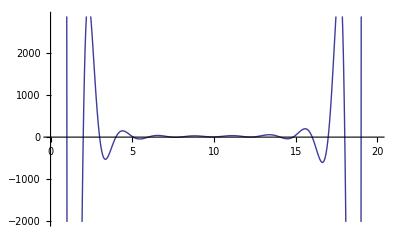

{{a_1→3080192,a_2→-15962162688187/1531530,a_3→71913597185536/4729725,a_4→-915331098535936/70945875,a_5→219224328810976/30405375,a_6→-1812576289134064/638512875,a_7→164477858608/200475,a_8→-113966124008/637875,a_9→133054766314/4465125,a_10→-17150463881/4465125,a_11→48952112/127575,a_12→-1454439824/49116375,a_13→1751584/1002375,a_14→-7054556/91216125,a_15→63424/25540515,a_16→-34856/638512875,a_17→67/91216125,a_18→-1/219287250}}

{3080192,-15962162688187/1531530,71913597185536/4729725,-915331098535936/70945875,219224328810976/30405375,-1812576289134064/638512875,164477858608/200475,-113966124008/637875,133054766314/4465125,-17150463881/4465125,48952112/127575,-1454439824/49116375,1751584/1002375,-7054556/91216125,63424/25540515,-34856/638512875,67/91216125,-1/219287250}

3080192-(15962162688187 j)/1531530+(71913597185536 j^2)/4729725-(915331098535936 j^3)/70945875+(219224328810976 j^4)/30405375-(1812576289134064 j^5)/638512875+(164477858608 j^6)/200475-(113966124008 j^7)/637875+(133054766314 j^8)/4465125-(17150463881 j^9)/4465125+(48952112 j^10)/127575-(1454439824 j^11)/49116375+(1751584 j^12)/1002375-(7054556 j^13)/91216125+(63424 j^14)/25540515-(34856 j^15)/638512875+(67 j^16)/91216125-j^17/219287250

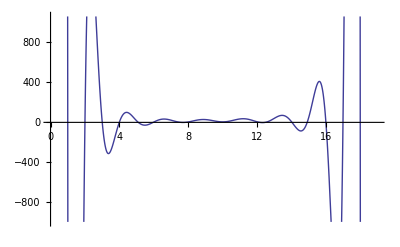

{{a_1→1458176,a_2→-62333972189/12870,a_3→32624132693632/4729725,a_4→-57583208475712/10135125,a_5→652014510710488/212837625,a_6→-1622194024328/1403325,a_7→445939829116/1403325,a_8→-41617511312/637875,a_9→90666330287/8930250,a_10→-307586423/255150,a_11→97495442/893025,a_12→-52486538/7016625,a_13→2673037/7016625,a_14→-254809/18243225,a_15→44474/127702575,a_16→-482/91216125,a_17→47/1277025750}}

{1458176,-62333972189/12870,32624132693632/4729725,-57583208475712/10135125,652014510710488/212837625,-1622194024328/1403325,445939829116/1403325,-41617511312/637875,90666330287/8930250,-307586423/255150,97495442/893025,-52486538/7016625,2673037/7016625,-254809/18243225,44474/127702575,-482/91216125,47/1277025750}

1458176-(62333972189 j)/12870+(32624132693632 j^2)/4729725-(57583208475712 j^3)/10135125+(652014510710488 j^4)/212837625-(1622194024328 j^5)/1403325+(445939829116 j^6)/1403325-(41617511312 j^7)/637875+(90666330287 j^8)/8930250-(307586423 j^9)/255150+(97495442 j^10)/893025-(52486538 j^11)/7016625+(2673037 j^12)/7016625-(254809 j^13)/18243225+(44474 j^14)/127702575-(482 j^15)/91216125+(47 j^16)/1277025750

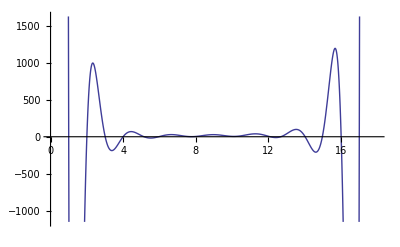

{{a_1→688128,a_2→-18345852929/8190,a_3→45218009344/14553,a_4→-175712781709568/70945875,a_5→3430423088/2673,a_6→-92575025176/200475,a_7→1700551016/14175,a_8→-2098893772/91125,a_9→196992349/59535,a_10→-637459489/1786050,a_11→174692/6075,a_12→-155258/91125,a_13→2246/31185,a_14→-37481/18243225,a_15→116/3274425,a_16→-178/638512875}}

{688128,-18345852929/8190,45218009344/14553,-175712781709568/70945875,3430423088/2673,-92575025176/200475,1700551016/14175,-2098893772/91125,196992349/59535,-637459489/1786050,174692/6075,-155258/91125,2246/31185,-37481/18243225,116/3274425,-178/638512875}

688128-(18345852929 j)/8190+(45218009344 j^2)/14553-(175712781709568 j^3)/70945875+(3430423088 j^4)/2673-(92575025176 j^5)/200475+(1700551016 j^6)/14175-(2098893772 j^7)/91125+(196992349 j^8)/59535-(637459489 j^9)/1786050+(174692 j^10)/6075-(155258 j^11)/91125+(2246 j^12)/31185-(37481 j^13)/18243225+(116 j^14)/3274425-(178 j^15)/638512875

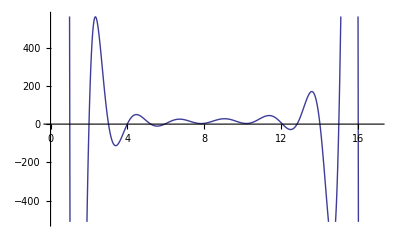

{{a_1→323584,a_2→-2380201853/2310,a_3→134002210816/96525,a_4→-55455417184/51975,a_5→49469529616/93555,a_6→-7667653688/42525,a_7→1867622312/42525,a_8→-331841998/42525,a_9→964643/945,a_10→-2783471/28350,a_11→291548/42525,a_12→-158066/467775,a_13→1042/93555,a_14→-103/467775,a_15→4/2027025}}

{323584,-2380201853/2310,134002210816/96525,-55455417184/51975,49469529616/93555,-7667653688/42525,1867622312/42525,-331841998/42525,964643/945,-2783471/28350,291548/42525,-158066/467775,1042/93555,-103/467775,4/2027025}

323584-(2380201853 j)/2310+(134002210816 j^2)/96525-(55455417184 j^3)/51975+(49469529616 j^4)/93555-(7667653688 j^5)/42525+(1867622312 j^6)/42525-(331841998 j^7)/42525+(964643 j^8)/945-(2783471 j^9)/28350+(291548 j^10)/42525-(158066 j^11)/467775+(1042 j^12)/93555-(103 j^13)/467775+(4 j^14)/2027025

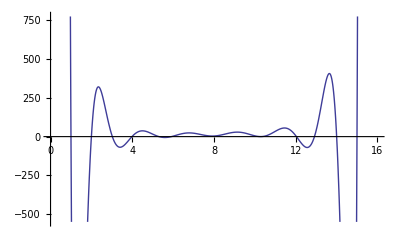

{{a_1→151552,a_2→-14144659801/30030,a_3→6386765312/10395,a_4→-23559082784/51975,a_5→1816587632/8505,a_6→-2912685848/42525,a_7→131689672/8505,a_8→-106824898/42525,a_9→166577/567,a_10→-696071/28350,a_11→2432/1701,a_12→-25766/467775,a_13→118/93555,a_14→-79/6081075}}

{151552,-14144659801/30030,6386765312/10395,-23559082784/51975,1816587632/8505,-2912685848/42525,131689672/8505,-106824898/42525,166577/567,-696071/28350,2432/1701,-25766/467775,118/93555,-79/6081075}

151552-(14144659801 j)/30030+(6386765312 j^2)/10395-(23559082784 j^3)/51975+(1816587632 j^4)/8505-(2912685848 j^5)/42525+(131689672 j^6)/8505-(106824898 j^7)/42525+(166577 j^8)/567-(696071 j^9)/28350+(2432 j^10)/1701-(25766 j^11)/467775+(118 j^12)/93555-(79 j^13)/6081075

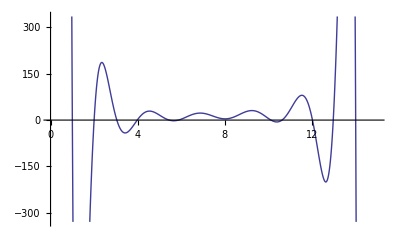

{{a_1→70656,a_2→-1481339767/6930,a_3→13975359488/51975,a_4→-2684443336/14175,a_5→3581829092/42525,a_6→-71310346/2835,a_7→221493751/42525,a_8→-3580481/4725,a_9→1094722/14175,a_10→-6121/1134,a_11→10477/42525,a_12→-1031/155925,a_13→37/467775}}

{70656,-1481339767/6930,13975359488/51975,-2684443336/14175,3581829092/42525,-71310346/2835,221493751/42525,-3580481/4725,1094722/14175,-6121/1134,10477/42525,-1031/155925,37/467775}

70656-(1481339767 j)/6930+(13975359488 j^2)/51975-(2684443336 j^3)/14175+(3581829092 j^4)/42525-(71310346 j^5)/2835+(221493751 j^6)/42525-(3580481 j^7)/4725+(1094722 j^8)/14175-(6121 j^9)/1134+(10477 j^10)/42525-(1031 j^11)/155925+(37 j^12)/467775

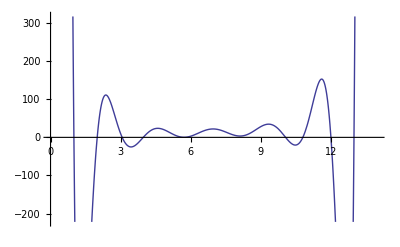

{{a_1→32768,a_2→-19044253/198,a_3→26123392/225,a_4→-157004672/2025,a_5→91414952/2835,a_6→-2788964/315,a_7→1113698/675,a_8→-141677/675,a_9→2423/135,a_10→-799/810,a_11→446/14175,a_12→-23/51975}}

{32768,-19044253/198,26123392/225,-157004672/2025,91414952/2835,-2788964/315,1113698/675,-141677/675,2423/135,-799/810,446/14175,-23/51975}

32768-(19044253 j)/198+(26123392 j^2)/225-(157004672 j^3)/2025+(91414952 j^4)/2835-(2788964 j^5)/315+(1113698 j^6)/675-(141677 j^7)/675+(2423 j^8)/135-(799 j^9)/810+(446 j^10)/14175-(23 j^11)/51975

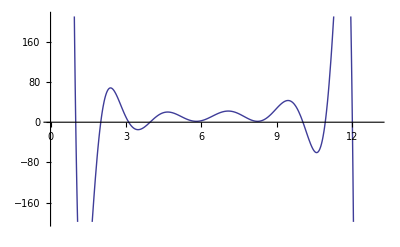

{{a_1→15104,a_2→-26989189/630,a_3→77678488/1575,a_4→-2507300/81,a_5→33711218/2835,a_6→-398363/135,a_7→325856/675,a_8→-9776/189,a_9→3299/945,a_10→-109/810,a_11→32/14175}}

{15104,-26989189/630,77678488/1575,-2507300/81,33711218/2835,-398363/135,325856/675,-9776/189,3299/945,-109/810,32/14175}

15104-(26989189 j)/630+(77678488 j^2)/1575-(2507300 j^3)/81+(33711218 j^4)/2835-(398363 j^5)/135+(325856 j^6)/675-(9776 j^7)/189+(3299 j^8)/945-(109 j^9)/810+(32 j^10)/14175

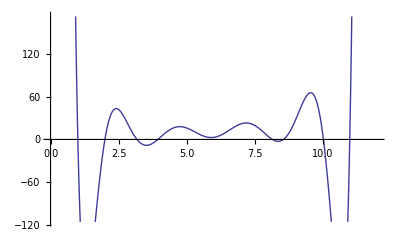

{{a_1→6912,a_2→-11872901/630,a_3→307928/15,a_4→-6786940/567,a_5→187982/45,a_6→-123451/135,a_7→5696/45,a_8→-2032/189,a_9→23/45,a_10→-59/5670}}

{6912,-11872901/630,307928/15,-6786940/567,187982/45,-123451/135,5696/45,-2032/189,23/45,-59/5670}

6912-(11872901 j)/630+(307928 j^2)/15-(6786940 j^3)/567+(187982 j^4)/45-(123451 j^5)/135+(5696 j^6)/45-(2032 j^7)/189+(23 j^8)/45-(59 j^9)/5670

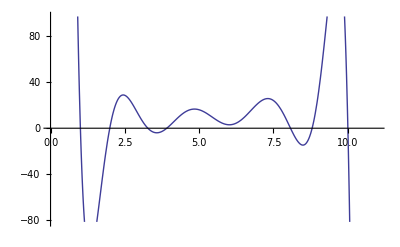

{{a_1→3136,a_2→-342875/42,a_3→2622638/315,a_4→-39956/9,a_5→123739/90,a_6→-4609/18,a_7→1271/45,a_8→-107/63,a_9→3/70}}

{3136,-342875/42,2622638/315,-39956/9,123739/90,-4609/18,1271/45,-107/63,3/70}

3136-(342875 j)/42+(2622638 j^2)/315-(39956 j^3)/9+(123739 j^4)/90-(4609 j^5)/18+(1271 j^6)/45-(107 j^7)/63+(3 j^8)/70

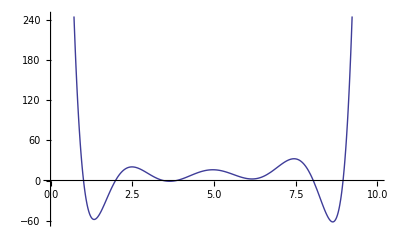

{{a_1→1408,a_2→-104017/30,a_3→146852/45,a_4→-70018/45,a_5→3715/9,a_6→-5549/90,a_7→218/45,a_8→-7/45}}

{1408,-104017/30,146852/45,-70018/45,3715/9,-5549/90,218/45,-7/45}

1408-(104017 j)/30+(146852 j^2)/45-(70018 j^3)/45+(3715 j^4)/9-(5549 j^5)/90+(218 j^6)/45-(7 j^7)/45

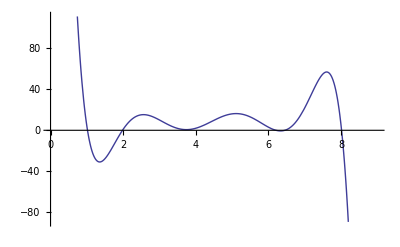

{{a_1→624,a_2→-43033/30,a_3→54928/45,a_4→-503,a_5→971/9,a_6→-347/30,a_7→22/45}}

{624,-43033/30,54928/45,-503,971/9,-347/30,22/45}

624-(43033 j)/30+(54928 j^2)/45-503 j^3+(971 j^4)/9-(347 j^5)/30+(22 j^6)/45

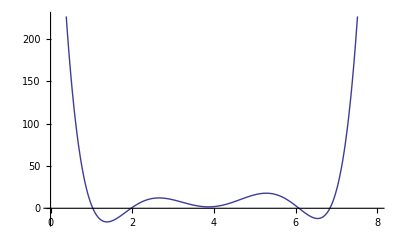

{{a_1→272,a_2→-17161/30,a_3→1280/3,a_4→-431/3,a_5→67/3,a_6→-13/10}}

{272,-17161/30,1280/3,-431/3,67/3,-13/10}

272-(17161 j)/30+(1280 j^2)/3-(431 j^3)/3+(67 j^4)/3-(13 j^5)/10

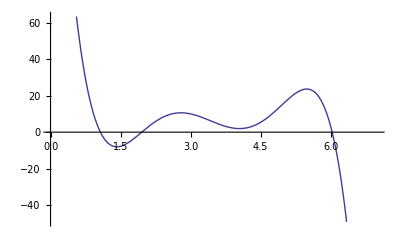

{{a_1→116,a_2→-1295/6,a_3→805/6,a_4→-199/6,a_5→17/6}}

{116,-1295/6,805/6,-199/6,17/6}

116-(1295 j)/6+(805 j^2)/6-(199 j^3)/6+(17 j^4)/6

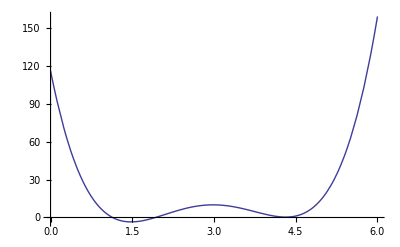

{{a_1→48,a_2→-445/6,a_3→35,a_4→-29/6}}

{48,-445/6,35,-29/6}

48-(445 j)/6+35 j^2-(29 j^3)/6

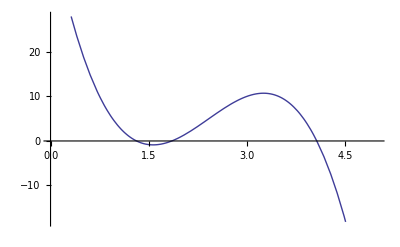

{{a_1→19,a_2→-21,a_3→6}}

{19,-21,6}

19-21 j+6 j^2

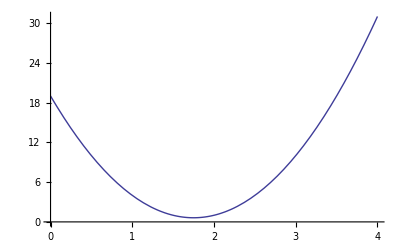

{{a_1→7,a_2→-3}}

{7,-3}

7-3 j

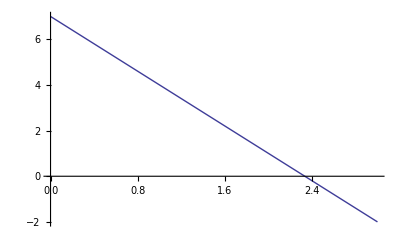

```mathematica
S:=Table[Piecewise[{{x/2, Mod[x,2]==0}, {3x+1, Mod[x,2]==1}}],{x,1,53}]
pn[S]
i[%]
po[%]
Plot[%,{j,0,(Length[%]+1)}]
```

```mathematica
s[j_]:=302867074940665856-(265105092950347706134396788345570497837 j)/193690281515374794150+(65896526873911761231209169453105633401208045568 j^2)/23148707568414059974597880625-(23602484031507742952630776335336581517307518386176 j^3)/6434290399682973733737911454375+(605453148171815834196134021900944378322493646808547328 j^4)/182511735646399397784868052600844975-(14679047676770615726554633348608194059419307680817217536 j^5)/6503529041698621074913284679781240625+(144378284637661269178129449073598783435206061760391501840384 j^6)/119502346141212162251531605990980296484375-(65391378122125365364358327015999276870313340058273098760192 j^7)/124587552359987147879256355182085841015625+(19302243864381680114698533137841088288555291684834675523584 j^8)/101935270112716757355755199694433869921875-(33850302576747201113319659653890635481050321286802178048 j^9)/586239188593954206094750400819150390625+(4138215078560991389777839867026954956391463172040216571543552 j^10)/274228036444536928755971868743178073974609375-(190666762570104071625936104609263103706097787578629226496 j^11)/55778975478582330074440003134418212890625+(793412628924757048675297354272457760215807943343365095424 j^12)/1171358485050228931563240065822782470703125-(7822353034458924586175403905753212507689777594744832 j^13)/66111746787757327320642454833779296875+(13724618517432055789916969225144025120507387493277696 j^14)/748395969354134401789809078107958984375-(14489949006733751112581885900228691294232423038107648 j^15)/5713943829513311861284097882062353515625+(13238860636532229522705586680492886191677585503142592512 j^16)/42117479967342621729525085488681607763671875-(1978849238594166030879198433679030569204417512448 j^17)/56431146131751058008211167865927734375+(634379231768493617928389582845616309363166296576 j^18)/179553646782844275480671897755224609375-(6889816925860341129753515761059282209393017750016 j^19)/21366883967158468782199955832871728515625+(119351486651851563109736771523789708978121071247616 j^20)/4465678749136119975479790769070191259765625-(796418668115988349063723062928252274520715456 j^21)/395018022922257406057478175061494140625+(36430031975113447550570906410270647743433260512 j^22)/262686985243301175028222986415893603515625-(136957849244165986162473870545025656774272 j^23)/15721287045502494166510442660595703125+(13931921789645482879800109165088594952164768 j^24)/27842399357584917168889993951914990234375-(35359468159492412083271446271386504636996 j^25)/1344115831055823587463654880437275390625+(50377299962198577052127756386125391762 j^26)/39766740563781762942711682853173828125-(53674380900255636666878135517342327626 j^27)/960082736468445419616896343169482421875+(17962612550218715017328391921823260134 j^28)/7942502638057139380467051566220263671875-(6065003257550827662270373922684044 j^29)/72317920409311473165948036238740234375+(396787187113694272487837206328914564 j^30)/139211996787924585844449969759574951171875-(4018881466601727448329593770054676 j^31)/45290859524707099142797066623429931640625+(3321354802912363607216861138648231 j^32)/1313434926216505875141114932079468017578125-(89925651030688940246506661917 j^33)/1364607715549616493653106422939707031250+(411970732375299489470415288334 j^34)/262686985243301175028222986415893603515625-(163222604595923327692848062 j^35)/4796647421198839930697949268603857421875+(22556475877209895224232726 j^36)/33576531948391879514885644880227001953125-(1231548836055219534979976 j^37)/102309667936864668168886847340926982421875+(13266521728682747460088 j^38)/67967961216798206126183569911804638671875-(208353059827079672 j^39)/73005328911705914206427035351025390625+(4734196746054227940032 j^40)/126352439902027865188575256466044823291015625-(102103687331515888 j^41)/232359274993637249281524355914233583984375+(260458581118700098 j^42)/56928022373441126073973467198987228076171875-(65384387442681322 j^43)/1557757703127798086206001238808650513720703125+(5759724985069138 j^44)/17135334734405778948266013626895155650927734375-(1136950437316 j^45)/489580992411593684236171817911290161455078125+(5373540989708 j^46)/394112698891332915810118313418588579971337890625-(25206710156 j^47)/378026466283523409042358382258646188952099609375+(63566858 j^48)/240562296725878533026955334164593029333154296875-(384301 j^49)/471502101582721924732832454962602337492982421875+(2474 j^50)/1347849042985951448040841217408686515702392578125-(4226 j^51)/1574480232070874998661422662107261376985494873046875+(274 j^52)/143277701118449624878189462251760785305680033447265625
```

```mathematica
Table[Table[Nest[s,x,y],{x,1,10}],{y,1,50}]
```

{{4,1,10,2,16,3,22,4,28,5},{2,4,5,1,8,10,11,2,14,16},{1,2,16,4,4,5,34,1,7,8},{4,1,8,2,2,16,17,4,22,4},{2,4,4,1,1,8,52,2,11,2},{1,2,2,4,4,4,26,1,34,1},{4,1,1,2,2,2,13,4,17,4},{2,4,4,1,1,1,40,2,52,2},{1,2,2,4,4,4,20,1,26,1},{4,1,1,2,2,2,10,4,13,4},{2,4,4,1,1,1,5,2,40,2},{1,2,2,4,4,4,16,1,20,1},{4,1,1,2,2,2,8,4,10,4},{2,4,4,1,1,1,4,2,5,2},{1,2,2,4,4,4,2,1,16,1},{4,1,1,2,2,2,1,4,8,4},{2,4,4,1,1,1,4,2,4,2},{1,2,2,4,4,4,2,1,2,1},{4,1,1,2,2,2,1,4,1,4},{2,4,4,1,1,1,4,2,4,2},{1,2,2,4,4,4,2,1,2,1},{4,1,1,2,2,2,1,4,1,4},{2,4,4,1,1,1,4,2,4,2},{1,2,2,4,4,4,2,1,2,1},{4,1,1,2,2,2,1,4,1,4},{2,4,4,1,1,1,4,2,4,2},{1,2,2,4,4,4,2,1,2,1},{4,1,1,2,2,2,1,4,1,4},{2,4,4,1,1,1,4,2,4,2},{1,2,2,4,4,4,2,1,2,1},{4,1,1,2,2,2,1,4,1,4},{2,4,4,1,1,1,4,2,4,2},{1,2,2,4,4,4,2,1,2,1},{4,1,1,2,2,2,1,4,1,4},{2,4,4,1,1,1,4,2,4,2},{1,2,2,4,4,4,2,1,2,1},{4,1,1,2,2,2,1,4,1,4},{2,4,4,1,1,1,4,2,4,2},{1,2,2,4,4,4,2,1,2,1},{4,1,1,2,2,2,1,4,1,4},{2,4,4,1,1,1,4,2,4,2},{1,2,2,4,4,4,2,1,2,1},{4,1,1,2,2,2,1,4,1,4},{2,4,4,1,1,1,4,2,4,2},{1,2,2,4,4,4,2,1,2,1},{4,1,1,2,2,2,1,4,1,4},{2,4,4,1,1,1,4,2,4,2},{1,2,2,4,4,4,2,1,2,1},{4,1,1,2,2,2,1,4,1,4},{2,4,4,1,1,1,4,2,4,2}}

```mathematica
Table[Nest[s,t,y],{y,1,10}]//Column
```

```mathematica
ArrayPlot[%]
```

-Graphics-

```mathematica
Monitor[Table[Nest[d,t,y],{t,1,1000},{y,0,100}],{y,x}]
ArrayPlot[%]
```

{{1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4},«998»,{1000,500,250,125,376,188,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53}}

```mathematica
d[x_]:=Piecewise[{{x/2, Mod[x,2]==0}, {3x+1, Mod[x,2]==1}}]
```

```mathematica
Table[d[x],{x,1,10}]
```

{4,1,10,2,16,3,22,4,28,5}

```mathematica
Map[d,%]
```

{2,4,5,1,8,10,11,2,14,16}

```mathematica
Map[d,%]
```

{1,2,16,4,4,5,34,1,7,8}

```mathematica
Map[d,%]
```

{4,1,8,2,2,16,17,4,22,4}

```mathematica
Map[d,%]
```

{2,4,4,1,1,8,52,2,11,2}

```mathematica
Map[d,%]
```

{1,2,2,4,4,4,26,1,34,1}

```mathematica
Map[d,%]
```

```mathematica
{4,1,1,2,2,2,13,4,17,4}
```

```mathematica
Map[d,%]
```

{2,4,4,1,1,1,40,2,52,2}

```mathematica
Map[d,%]
```

{1,2,2,4,4,4,20,1,26,1}

```mathematica
Map[d,%]
```

{4,1,1,2,2,2,10,4,13,4}

```mathematica
Map[d,%]
```

{2,4,4,1,1,1,5,2,40,2}

```mathematica
Map[d,%]
```

{1,2,2,4,4,4,16,1,20,1}

```mathematica
Map[d,%]
```

{4,1,1,2,2,2,8,4,10,4}

```mathematica
Map[d,%]
```

{2,4,4,1,1,1,4,2,5,2}

```mathematica
Map[d,%]
```

{1,2,2,4,4,4,2,1,16,1}

```mathematica
Map[d,%]
```

{4,1,1,2,2,2,1,4,8,4}

```mathematica
Map[d,%]
```

{2,4,4,1,1,1,4,2,4,2}

```mathematica
Map[d,%]
```

{1,2,2,4,4,4,2,1,2,1}

```mathematica
Map[d,%]
```

{4,1,1,2,2,2,1,4,1,4}

```mathematica
Map[d,%]
```

{2,4,4,1,1,1,4,2,4,2}

```mathematica
(0.45+0.01)((.15)^2+2*.15*.003)/2
(0.45-0.01)((.15)^2-2*.15*.003)/2
```

0.005382

0.004752

```mathematica
(0.00538+0.00475)/2
```

0.005065

```mathematica
{0.00538,0.00475}-%
```

{0.000315,-0.000315}

```mathematica
(0.00577+0.00065)/(0.00507-0.00032)
(0.00577-0.00065)/(0.00507+0.00032)
```

1.35158

0.949907

```mathematica
(1.35+0.950)/2
```

1.15

```mathematica
{1.35,0.950}-%
```

{0.2,-0.2}

```mathematica
Solve[D[n-Log[n],n]==0,n]
```

{{n→1}}

{1,1,1,1,1,1,289/343,509/536,1747/1801,1238/1265,2719/3259,862/997,3691/4717,281/389,4663/6175,1403/1592,17785/19297,1739/1847,26533/32419,16547/19490,35281/45541,18734/26051,«4957»,61099672642657/79499761143865,244681120107109/318281474111941,122481774821795/159281951824211,244974009996793/318846333184903,122628219766637/159564381360692,49107773813951/63882238451573,122910649303118/159846810897173,245852679665845/319976051330827,123067554601163/160129240433654,246166490261935/320540910403789,123088475307569/160411669970135,246459380151619/321105769476751,61685452422025/80347049753308,247024239224581/321670628549713,123653334380531/160976529043097,247400811939889/322235487622675,123841620738185/161258958579578,247777384655197/322800346695637,123935763917012/161541388116059,248153957370505/323365205768599,124218193453493/161823817652540}

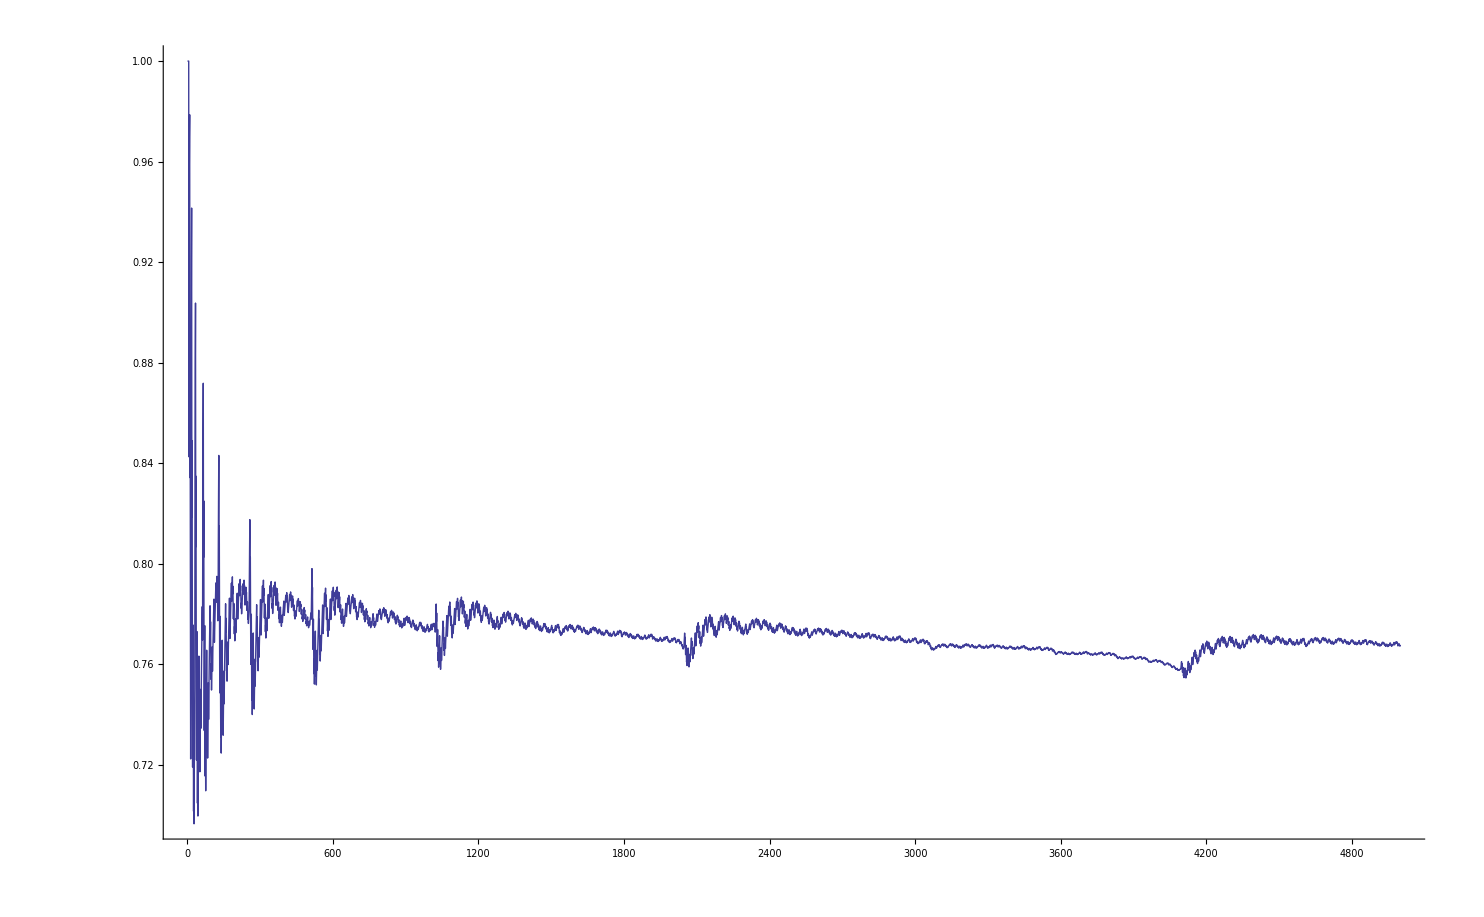

```mathematica
Monitor[Table[Mean[Table[Denominator[FromDigits[IntegerDigits[x,2]]/9^Length[IntegerDigits[x,2]]],{x,1,y}]]/Mean[Table[Denominator[1/9^Length[IntegerDigits[x,2]]],{x,1,y}]],{y,1,5000}],{x,y}]
ListPlot[%,Joined->True]
```

```mathematica
Monitor[Mean[Table[Denominator[FromDigits[IntegerDigits[y,2]]/9^Length[IntegerDigits[y,2]]],{y,1,10000000}]]/Mean[Table[Denominator[1/9^Length[IntegerDigits[x,2]]],{x,1,10000000}]],{x,y}]
```

```mathematica
N[1400918516056056742167101347/1865507136391308081102048244]
```

0.750959

```mathematica
N[252837136230530948054411/342139312918666562710100]
```

0.738989

```mathematica
N[552715666432820/727889446207889]
```

0.75934

```mathematica
FromDigits[IntegerDigits[y,2]]
```

```mathematica
∑_(i=0)^(n-1) 9*10^i
```

-1+10^n

```mathematica
Table[GCD[FromDigits[IntegerDigits[y,2]],(-1+10^Length[IntegerDigits[y,2]])],{y,1,1000}]
```

{1,1,11,1,1,1,111,1,11,101,3,11,3,3,1111,1,1,1,3,1,3,3,1,1,3,3,1,3,1,1,11111,1,11,1,111,1001,3,3,11,1,3,10101,1,3,1001,1,1,11,111,3,11,3,1,1001,1,111,11,1,1,11,1,1,111111,1,1,1,3,1,3,3,1,1,3,3,1,3,1,1,1,1,3,3,1,3,1,1,1,3,1,1,1,1,1,1,3,1,3,3,1,3,1,1,1,3,1,1,1,1,1,1,3,3,1,1,1,1,1,1,3,1,1,1,3,1,3,3,1111111,1,11,101,3,11,3,3,1111,10001,3,3,1,3,11,1,1,11,3,3,11,3,1,1111,1,3,110011,1,1,11,1,1,33,101,3,3,1,3,1111,1,1,3,1,1010101,1,1,1,1,303,3,11,1,1,1111,1,1,33,1,1,1,30003,1,33,303,1,11,3,3,1111,3,1,11,1,3,11,1,1,110011,1,1,33,3,1,1111,1,1,1,1,303,11,1,1,33,1,30003,33,1,3,1111,1,1,11,1,1,33,1,1,1,303,1,33,30003,1,1111,1,1,33,1,303,33,1,1,33,303,1,33,1,1,11111111,1,1,1,111,1,3,3,1,1,3,111,1,3,1,1,1,1,111,3,1,3,1,1,1,111,1,1,1,1,1,1,111,1,3,3,1,1001001,1,1,1,3,1,1,1,1,1,1,3,3,1,1,1,1,1,1,3,1,1,1,111,1,3,3,1,1,3,111,1,3,1,1,1,3,1,1,1,1,1,1,3,111,1,1,1,1,1,1,111,1,1,1,3,1,3,111,1,3,1,1,1,1,1,1,3,1,1,1,3,1,1001001,3,1,1,1,1,111,1,3,3,1,1,3,111,1,3,1,1,1,1,111,3,1,3,1,1,1,111,1,1,1,1,1,1,111,3,1,1,1,1,1,1,3,1,1,1,3,1,111,3,1,3,1,1,1,1,1,1,3,1,1,1,111,1,3,3,1,1,1,1,3,1,3,1001001,1,1,111,3,1,3,1,1,1,111,1,1,1,1,1,1,111,1,1,1,3,1,3,111,1,1,1,1,3,1,111,3,1,1,3,3,1,111,1,1,1,1,1,1,111,1,3,3,1,1,3,111,1,3,1,1,1,1,111,3,1,3,1,1,1,111,1,1,1,1,1,1,111111111,1,11,1,3,11,3,3,11,1,3,3,1,3,11,1,11111,100001,3,3,11,3,1,11,1,3,11,1,1,11,1,1,33,1,3,3,1,3,11,1,1,3,1,1,1,1,1,11111,3,3,100001,1,1,11,1,1,33,1,1,1,3,1,33,3,1,11,3,3,11,3,1,11,1,3,11,1,1,11,11111,1,33,3,1,100001,1,1,1,1,3,11,1,1,33,1,3,33,1,3,11,1,1,11,1,1,33,1,1,1,3,11111,33,3,1,11,1,1,300003,1,3,33,1,1,33,3,1,33,1,1,11,1,3,3,1,3,11,1,1,3,1,1,11111,1,1,1,3,3,11,1,1,100001,1,1,33,1,1,1,3,1,33,3,1,3,1,1,1,1,1,1,3,1,1,101010101,3,1,3,3,1,1,1,1,3,1,300003,3,1,1,3,3,1,3,1,1,1,3,11,1,1,11,1,1,33,1,11111,1,3,1,33,3,1,11,1,1,33,1,3,300003,1,1,33,3,1,33,1,1,11,1,1,1,3,1,33,3,1,11111,3,3,1,3,1,1,1,1,33,3,1,33,1,1,100001,3,1,1,1,1,11,1,9,11,3,3,11,3,1,11,11111,3,11,1,1,11,1,1,33,3,1,11,1,1,1,1,3,100001,1,1,33,1,3,33,1,3,11,1,1,11,1,11111,33,1,1,1,3,1,33,3,1,11,1,1,33,1,3,33,1,1,300003,3,1,33,1,1,11,3,1,11,1,1,11111,1,3,11,1,1,33,1,3,33,1,1,1,1,3,1,3,3,1,1,3,300003,1,3,1,1,1,11,1,1,33,11111,3,33,1,1,33,3,1,33,1,1,11,1,3,33,1,3,1,1,1,33,1,1,100001,1,1,11,9,3,11,1,11111,11,1,1,33,1,1,1,3,1,33,3,1,11,1,1,33,1,3,33,1,1,33,3,1,300003,1,1,11,1,1,11111,3,1,33,3,1,1,3,3,1,3,1,1,1,1,33,3,1,33,1,1,11,3,1,1,1,1,100001,1,9,11,11111,1,33,1,3,33,1,1,33,3,1,33,1,1,11,1,3,33,1,3,1,1,1,33,1,1,11,1,1,100001,9,11111,33,3,1,33,1,1,11,3}

```mathematica
snd[x_]:=x[[2]]
```

```mathematica
FactorInteger[145432]
```

```mathematica
Table[Total[Map[snd,FactorInteger[x]]],{x,1,100}]
```

{1,1,1,2,1,2,1,3,2,2,1,3,1,2,2,4,1,3,1,3,2,2,1,4,2,2,3,3,1,3,1,5,2,2,2,4,1,2,2,4,1,3,1,3,3,2,1,5,2,3,2,3,1,4,2,4,2,2,1,4,1,2,3,6,2,3,1,3,2,3,1,5,1,2,3,3,2,3,1,5,4,2,1,4,2,2,2,4,1,4,2,3,2,2,2,6,1,3,3,4}

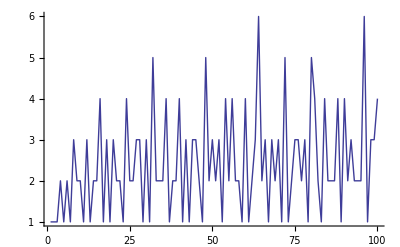

```mathematica
ListPlot[%,Joined->True]
```

```mathematica
Monitor[Table[Total[Map[snd,FactorInteger[GCD[FromDigits[IntegerDigits[y,2]],(-1+10^Length[IntegerDigits[y,2]])]]]],{y,1,1000000}],y]
```

{1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,3,1,1,1,1,1,4,1,1,3,1,1,1,2,1,1,1,1,3,1,2,1,1,1,1,1,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,3,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,3,1,1,1,1,2,1,1,1,1,2,1,1,2,1,1,1,3,1,2,2,1,1,1,1,2,1,1,1,1,1,1,«999598»,1,1,1,1,1,2,1,1,1,1,2,2,1,2,2,1,1,2,2,1,2,1,1,1,1,2,2,1,2,1,1,1,3,1,1,1,1,1,1,1,2,2,2,3,2,1,1,1,2,1,1,1,1,1,1,3,2,1,1,1,1,1,1,1,1,1,1,2,1,1,3,1,1,2,2,1,2,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,3,1,1,2,1,1,1,1,1,1,2,1,1,1,1,3,1,1,1,1,1,2,1,1,1,1,1,1,2,1,2,1,2,1,2,2,1,1,1,1,2,1,2,2,1,2,2,2,1,2,1,2,1,1,1,1,2,1,2,2,1,1,2,2,1,2,1,1,1,1,2,2,1,2,1,1,1,2,1,1,1,1,1,1,3,1}

```mathematica
ListPlot[%,Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Mean[{{}, {{1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,3,1,1,1,1,1,4,1,1,3,1,1,1,2,1,1,1,1,3,1,2,1,1,1,1,1,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,3,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,3,1,1,1,1,2,1,1,1,1,2,1,1,2,1,1,1,3,1,2,2,1,1,1,1,2,1,1,1,1,1,1,«999598»,1,1,1,1,1,2,1,1,1,1,2,2,1,2,2,1,1,2,2,1,2,1,1,1,1,2,2,1,2,1,1,1,3,1,1,1,1,1,1,1,2,2,2,3,2,1,1,1,2,1,1,1,1,1,1,3,2,1,1,1,1,1,1,1,1,1,1,2,1,1,3,1,1,2,2,1,2,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,3,1,1,1,1,1,1,1,1,1,3,1,1,2,1,1,1,1,1,1,2,1,1,1,1,3,1,1,1,1,1,2,1,1,1,1,1,1,2,1,2,1,2,1,2,2,1,1,1,1,2,1,2,2,1,2,2,2,1,2,1,2,1,1,1,1,2,1,2,2,1,1,2,2,1,2,1,1,1,1,2,2,1,2,1,1,1,2,1,1,1,1,1,1,3,1}}, {}}]
```

```mathematica
N[639431/500000]
```

1.27886

```mathematica
Monitor[Table[Total[Map[snd,FactorInteger[GCD[FromDigits[IntegerDigits[y,2]],(-1+10^Length[IntegerDigits[y,2]])]]]],{y,1,10000000}],y]
ListPlot[%,Joined->True,PlotRange->All]
```

{1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,3,1,1,1,1,1,4,1,1,3,1,1,1,2,1,1,1,1,3,1,2,1,1,1,1,1,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,3,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,3,1,1,1,1,2,1,1,1,1,2,1,1,2,1,1,1,3,1,2,2,1,1,1,1,2,1,1,1,1,1,1,«9999598»,1,5,1,1,2,1,1,1,3,1,1,1,1,1,1,2,1,1,1,2,1,1,3,1,1,1,1,2,1,2,1,1,1,1,2,1,2,1,1,1,1,1,1,3,1,2,2,1,1,2,2,1,2,1,1,1,1,2,2,1,1,1,1,1,5,1,1,1,1,1,1,2,1,3,1,2,1,3,3,1,1,2,2,1,4,1,1,1,1,2,3,3,3,1,1,1,2,1,1,1,1,1,1,2,1,3,5,1,2,3,1,1,3,1,1,2,1,1,1,1,3,1,1,1,2,1,1,5,1,1,1,1,1,2,2,1,3,2,2,1,3,1,1,1,2,3,1,1,1,1,1,2,2,1,3,1,1,2,1,1,1,1,1,4,1,1,2,1,3,1,1,1,3,1,1,3,1,1,2,1,1,4,1,1,1,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1}

-Graphics-

```mathematica
Mean[{{}, {{1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,3,1,1,1,1,1,4,1,1,3,1,1,1,2,1,1,1,1,3,1,2,1,1,1,1,1,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,3,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,3,1,1,1,1,2,1,1,1,1,2,1,1,2,1,1,1,3,1,2,2,1,1,1,1,2,1,1,1,1,1,1,«9999598»,1,5,1,1,2,1,1,1,3,1,1,1,1,1,1,2,1,1,1,2,1,1,3,1,1,1,1,2,1,2,1,1,1,1,2,1,2,1,1,1,1,1,1,3,1,2,2,1,1,2,2,1,2,1,1,1,1,2,2,1,1,1,1,1,5,1,1,1,1,1,1,2,1,3,1,2,1,3,3,1,1,2,2,1,4,1,1,1,1,2,3,3,3,1,1,1,2,1,1,1,1,1,1,2,1,3,5,1,2,3,1,1,3,1,1,2,1,1,1,1,3,1,1,1,2,1,1,5,1,1,1,1,1,2,2,1,3,2,2,1,3,1,1,1,2,3,1,1,1,1,1,2,2,1,3,1,1,2,1,1,1,1,1,4,1,1,2,1,3,1,1,1,3,1,1,3,1,1,2,1,1,4,1,1,1,1,1,2,1,1,7,1,1,2,1,1,2,1,1,3,1}}, {}}]
```

```mathematica
N[2991303/2500000]
```

1.19652

```mathematica
Monitor[Table[Total[Map[snd,FactorInteger[GCD[FromDigits[IntegerDigits[y,2]],(-1+10^Length[IntegerDigits[y,2]])]]]],{y,10000001,20000000}],y]
ListPlot[%,Joined->True,PlotRange->All]
```

```mathematica
{{}, {{2,3,1,3,1,1,1,2,1,1,1,1,1,1,2,3,3,1,1,1,1,1,2,1,1,1,1,1,2,1,1,5,1,1,1,1,1,1,2,1,2,1,1,1,1,2,1,1,1,2,1,1,5,1,1,1,1,1,2,3,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,2,2,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,1,1,1,1,1,1,2,2,1,2,1,1,1,1,1,1,1,1,2,1,1,5,1,1,1,1,1,2,1,1,3,1,1,1,3,3,1,2,1,1,1,4,1,1,1,1,1,2,2,3,1,1,1,1,1,1,2,1,1,1,2,1,2,3,1,2,3,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,5,1,1,2,1,1,2,2,1,2,1,1,1,3,1,1,1,1,1,1,1,1,1,«9999598»,1,1,1,1,1,1,1,1,1,2,2,1,2,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,2,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}, {}}
```

-Graphics-

```mathematica
Mean[{{}, {{2,3,1,3,1,1,1,2,1,1,1,1,1,1,2,3,3,1,1,1,1,1,2,1,1,1,1,1,2,1,1,5,1,1,1,1,1,1,2,1,2,1,1,1,1,2,1,1,1,2,1,1,5,1,1,1,1,1,2,3,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,2,2,1,3,1,1,2,1,1,2,1,1,4,1,1,2,1,1,1,1,1,1,1,1,2,2,1,2,1,1,1,1,1,1,1,1,2,1,1,5,1,1,1,1,1,2,1,1,3,1,1,1,3,3,1,2,1,1,1,4,1,1,1,1,1,2,2,3,1,1,1,1,1,1,2,1,1,1,2,1,2,3,1,2,3,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,5,1,1,2,1,1,2,2,1,2,1,1,1,3,1,1,1,1,1,1,1,1,1,«9999598»,1,1,1,1,1,1,1,1,1,2,2,1,2,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,2,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}, {}}]
```

```mathematica
N[(398167/312500+2991303/2500000)/2]
```

1.23533

```mathematica
Table[FactorInteger[10^i-1],{i,1,15}]//Column
```

{{3,2}}
{{3,2},{11,1}}
{{3,3},{37,1}}
{{3,2},{11,1},{101,1}}
{{3,2},{41,1},{271,1}}
{{3,3},{7,1},{11,1},{13,1},{37,1}}
{{3,2},{239,1},{4649,1}}
{{3,2},{11,1},{73,1},{101,1},{137,1}}
{{3,4},{37,1},{333667,1}}
{{3,2},{11,1},{41,1},{271,1},{9091,1}}
{{3,2},{21649,1},{513239,1}}
{{3,3},{7,1},{11,1},{13,1},{37,1},{101,1},{9901,1}}
{{3,2},{53,1},{79,1},{265371653,1}}
{{3,2},{11,1},{239,1},{4649,1},{909091,1}}
{{3,3},{31,1},{37,1},{41,1},{271,1},{2906161,1}}

```mathematica
Table[IntegerQ[((j)^i-1)/(j-1)],{i,1,25},{j,2,25}]
```

{{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}}

```mathematica
GraphPlot3D[With[{rules=MapIndexed[{First[#2],#[[1,2]],#[[2,#[[1,2]]]]}&,TuringMachine[1507,{1,RandomInteger[1,30]},200]]},Join[Rule@@@Partition[rules,2,1],Flatten[Rule@@@Partition[#,2,1]&/@Last@Reap[Sow[#,#[[2]]]&/@rules],1]]]]
```

-Graphics3D-

```mathematica
RSolve[{-2 d[n-1]+1==d[n]},d[n],n]
```

{{d[n]→1/3 (1-(-2)^n)+(-2)^(-1+n) C[1]}}

```mathematica
numtmrules[numstates_Integer,numcolors_Integer]:=(numstates*numcolors)^(2*numstates*numcolors)
```

```mathematica
numtmrules[2,3]
```

2176782336

```mathematica
steps:=50
machine:=4095
Monitor[Table[ArrayPlot[Last/@TuringMachine[n,{1,{{},0}},steps],ImageSize->{Automatic,80}],{n,1,machine}],n]
```

```mathematica
Log2[(1+FromDigits[Last /@ TuringMachine[1154,{1,{{},0}},100],2])]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
FromDigits[Last /@ TuringMachine[{169850843303314304904918,4,4},{1,{{},0}},50000]]
```

{«1»}

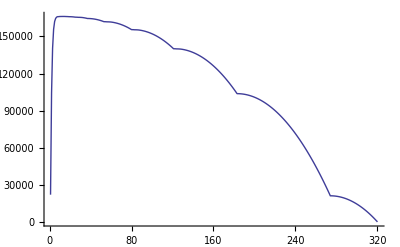

```mathematica
ListPlot[Log2[%],Joined->True]
```

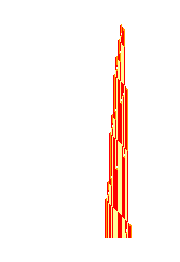
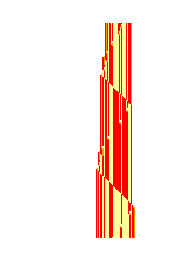
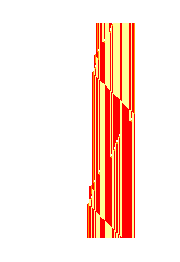
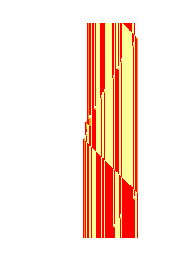
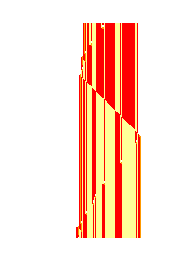
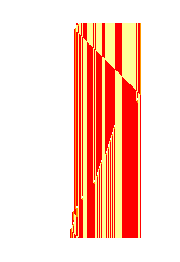
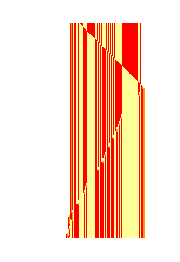
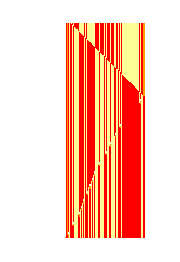

```mathematica
$TMColors={0->White,1->ColorData["WebSafe"]["#ffff99"],2->ColorData["WebSafe"]["#ff9900"],3->ColorData["WebSafe"]["#FF0000"]};
e=TuringMachine[{348371888147308385687045,4,4},{1,{{},0}},5000];
Row[ArrayPlot[#,ColorRules->$TMColors,ImageSize->180]&/@Partition[e[[All,2]],200]]
```

```mathematica
348371888147308385687045
```

```mathematica
t = FromDigits[Last /@ TuringMachine[{348371888147308385687045,4,4},{1,{{},0}},100000],2];
```

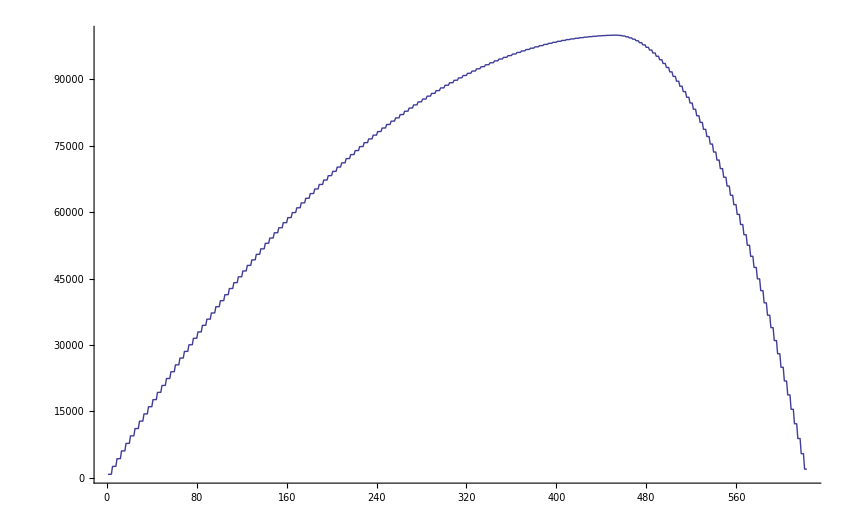

```mathematica
ListPlot[Log2[t],Joined->True]
```